```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_]:=Cos[x]Sin[x]
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fourth_order_pde/biharmonic_equation/solution/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

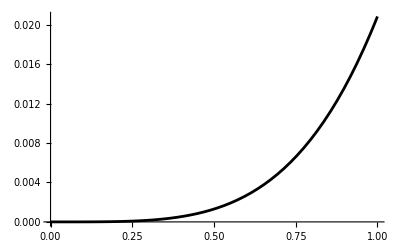

```mathematica
plotuexact=Plot[u[x],{x,xl,xr},PlotRange->Full,PlotStyle->Black]
```

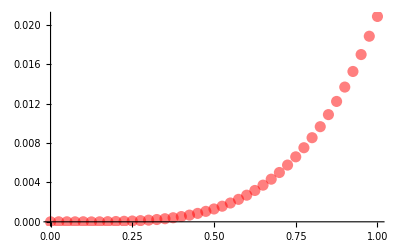

```mathematica
plotunum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.5],PointSize->0.02}]
```

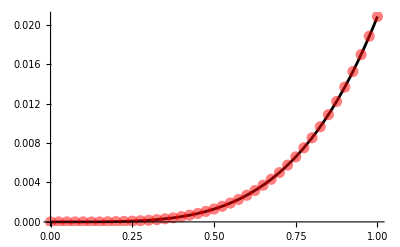

```mathematica
Show[plotuexact,plotunum]
```